# Basics From Calculus

## Derivatives and Finite Differences

For f:ℝ→ℝ and x∈ℝ
	f'[x]=lim_(h->0) (f[x+h]-f[x])/h

For f:ℝ^n→ℝ and and x,u∈ℝ^n
	∂_u f | = | lim_(h->0) (f[x+ h u ]-f[x])/h
(∂f)/(∂x_i) | = | lim_(h->0) (f[x+ h e_i ]-f[x])/h
Df | = | {∂_1 f,∂_2 f,…,∂_n f}
where ∂_i f=∂f/∂x_i and we have skipped writing down the x dependence.

A derivative of a derivative is a second derivative.  The Hessian of  f:ℝ^n→ℝ 
is the n×n symmetric matrix of second derivatives
	(∂f)/(∂x_i∂x_j) | = | ∂_i (∂_j f) | = | ∂_j (∂_i f)
DDf_(i,j) | = | H_(i,j) | = | ∂_ij f  
Calculus courses usually cover finite Difference(FD) approximations

  | Forward Diff | Centered Diff
f'[x] | (f[x+h]-f[x])/h | (f[x+h]-f[x-h])/(2h)
f''[x] | (f[x+2h]-2f[x+h]+f[x])/h^2  | (f[x+h]-2f[x]+f[x-h])/h^2
∂_i f[x] | (f[x+he_i]-f[x])/h | (f[x+he_i]-f[x-he_i])/(2h)
∂_(i,j) f[x] | (f[x+he_i+ he_j]-f[x+he_i]- f[x+he_j]+ f[x])/h^2 | (f[x+he_i+ he_j]-f[x+he_i-he_j]- f[x+he_j-he_i]+ f[x-he_i-he_j])/h^2

Taylor Series (TS) show that centered differences are more accurate with error behavior described by the TS error terms.

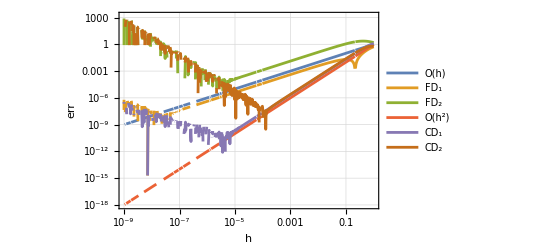

```mathematica
f[x_]:= Cos[x + Exp[ Sin[Log[1+x^2]]]]
x=1.5;
SetOptions[LogLogPlot,GridLines->Automatic,MaxRecursion->4,Frame->True];
LogLogPlot[{
h,Abs[f'[x]-(f[x+h]-f[x])/h],Abs[f''[x]-(f[x+2h]-2f[x+h]+f[x])/h^2],
h^2,Abs[f'[x]-(f[x+h]-f[x-h])/(2h)],Abs[f''[x]-(f[x+h]-2f[x]+f[x-h])/h^2]
},{h,10^-9, 1},
FrameLabel->{"h","err"},
PlotLegends->{"O(h)","FD_1","FD_2","O(h^2)","CD_1","CD_2"}]
```

## Taylor Series

For f:ℝ→ℝ
	f[x_0+h]=f[x_0]+h f'[x_0]+1/2 h^2 f''[x_0]+O(h^3)
For f:ℝ^n→ℝ and u∈ℝ^n
	f[x_0+h u]=f[x_0]+h g_0.u+1/2 h^2 u.H_0.u+O(h^3)
where g_0=Df[x_0] and H_0=DDf[x_0].

A critical point of f:ℝ^n→ℝ satisfies g=Df[x_*]=0_n. 
 A critical point of f is a local minimum if H=DDf[x_*] is positive definite.   
 A critical point of f is a saddle if H=DDf[x_*] is indefinite.

```mathematica
n=2;
{λ1,λ2}={1.2,-1.3};
Q=Orthogonalize[RandomReal[{-1,1},{n,n}]];
H=Q.DiagonalMatrix[{λ1,λ2}].Qᵀ;
TabView[{
"H"->MatrixForm[H],
"3D"->Plot3D[ 1/2{x1,x2}.H.{x1,x2},{x1,-1,1},{x2,-1,1}],
"Cont"->ContourPlot[ 1/2{x1,x2}.H.{x1,x2},{x1,-1,1},{x2,-1,1}]
},2]
```

123

```mathematica
n=3;
{λ1,λ2,λ3}={1.2,1.3,0.5};
Q=Orthogonalize[RandomReal[{-1,1},{n,n}]];
H=Q.DiagonalMatrix[{λ1,λ2,λ3}].Qᵀ;
TabView[{
"H"->MatrixForm[H],
"Cont"->ContourPlot3D[ 1/2{x1,x2,x3}.H.{x1,x2,x3},{x1,-1,1},{x2,-1,1},{x3,-1,1},Contours->10,PlotLegends->Automatic,
PlotLabel->Eigenvalues[H]]
},2]
```

12

## Constrained and Unconstrained Optimization

Our target is to minimize an objective function f[x] subject to some equality constraints c_i[x]=0 for i∈ℰ and some inequality constraints c_i[x]≥0 for i∈ℐ.  The c stands for constraint. The script ℰ stands for Equality. The script ℐ stands for inequality.

We are going to assume throughout that the objective function f and all the constraint functions c are differentiable. The feasible set
	Ω={x:c_i[x]=0 for i∈ℰ and c_i[x]≥0for i∈ℐ} 
does not need to have a smooth boundary.

We seek 
	f^*=min_(x∈Ω) f[x] 
and more importantly the x^* that gives f^*=f[x^*].  It is common in papers and code to write 
	x^*=argmin_(x∈Ω)f[x].
Simple box constraints 
	l_i≤x_i≤u_i for i=1 to n
are usually specified and treated separately in algorithms and code. The mnemonic is l for lower and u for upper.  If l_1=-∞ and u_1=+∞ then 
 	-∞<=x_1≤∞
 has no effect.

Any number of inequality constraints makes sense. More than n equality constraints does not really make sense.

### Constraint Pics

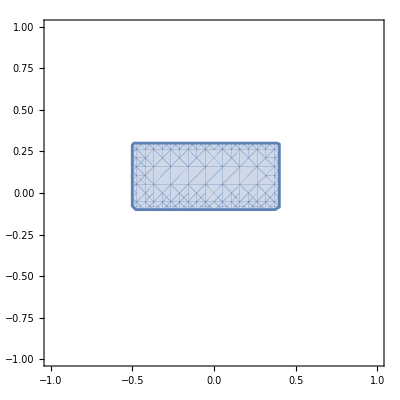

```mathematica
RegionPlot[And[-0.5<x1<0.4,-0.1<x2<0.3],{x1,-1,1},{x2,-1,1}]
```

```mathematica
RegionPlot3D[And[-0.5<x1<0.4,-0.1<x2<0.3, 0.1<x3<0.2],{x1,-1,1},{x2,-1,1},{x3,-1,1},PlotPoints->40]
```

-Graphics3D-

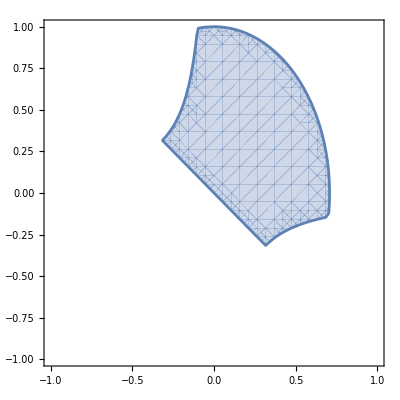

```mathematica
RegionPlot[And[1-( 2 x1^2+x2^2)>0,0.1+x1*x2>0,x1+x2>0],{x1,-1,1},{x2,-1,1}]
```

```mathematica
RegionPlot3D[And[x1+x2+x3>0,
1-( 2 x1^2+x2^2)>0,0.1+x1*x2>0,x1+x2>0],{x1,-1,1},{x2,-1,1},{x3,-2,2},
PlotPoints->40]
```

-Graphics3D-

```mathematica
RegionPlot3D[And[-0.3<x1+x2+x3<0.3,
1-( 2 x1^2+x2^2)>0,0.1+x1*x2>0,x1+x2>0,-0.1+x1+x2+x3>0],{x1,-1,1},{x2,-1,1},{x3,-2,2},
PlotPoints->40]
```

-Graphics3D-

```mathematica
RegionPlot3D[And[-0.3<x1+x2+x3<0.3,
1-( 2 x1^2+x2^2)>0,0.1+x1*x2>0,x1+x2>0,10.1+x1+x2+x3>0],{x1,-1,1},{x2,-1,1},{x3,-2,2},
PlotPoints->40]
```

-Graphics3D-

## Definitions for Unconstrained Optimization

For f:ℝ^n→ℝ and no constraints argmin f[x]
	x^* is a global min if f[x^*]≤f[x] for all x
	x^* is a strict global min if f[x^*]<f[x] for all x≠x_*
	x^* is a local min if f[x^*]≤f[x^*+u] for all ||u||≤ϵ
	x^* is a strict local min if f[x^*]≤f[x^*+u] all 0< ||u||≤ϵ

A function f:ℝ^n→ℝ is convex if for 0≤α≤1
	f[α x +(1-α)y]≤α f[x]+(1-a)f[y]. 
It is strictly convex if for 0<α<1 and x≠y
	f[α x +(1-α)y]<α f[x]+(1-a)f[y]

## Definitions for Constrained Optimization

For f:ℝ^n→ℝ and no constraints argmin_(x∈ Ω) f[x] if x^* is feasible i.e. x^*∈Ω then
	x^* is a global min if f[x^*]≤f[x] for all x∈Ω
	x^* is a strict global min if f[x^*]<f[x] for all x∈Ω and x≠x_*
	x^* is a local min if f[x^*]≤f[x^*+u] for all ||u||≤ϵ with x^*+u∈Ω
	x^* is a strict local min if f[x^*]≤f[x^*+u] all 0< ||u||≤ϵ withx^*+u∈Ω

When it comes to writing down equations we will have some technical conditions on the faces, edges, and corners etc of the feasible set Ω.

## Theorems for Unconstrained Optimization (Calculus II and III)

1) If f:ℝ^n→ℝ is smooth a local minimizer of f satisfies Df(x^*)=0 and the Hessian H=DDf[x^*] has no negative eigenvalues. 
2) If f:ℝ^n→ℝ is smooth and Df(x^*)=0 and the Hessian H=DDf[x^*] has all positive eigenvalues then x^* is a strict local minimizer of f.
Critical points satisfy Df(x)=0. Symmetric matrices with all positive eigenvalues are SPD (Symmetric Positive Definite). Symmetric matrices with no negative eigenvalues are Symmetric Semi Positive Definite which is sometimes abbreviated to SSPD.

Df(x^*)=0 is a first order optimality condition.  Critical Points (CP) satisfy Df(x^*)=0

Second order optimality conditions involve the Hessian DDf(x^*)

Unconstrained optimization algorithms try to find critical points with SPD Hessians.   All such points are local minimizer.  Unless there is a tie only one of these points is a global minimizer!  Our algorithms will try to compute local minimizers.

## Theorems for Constrained Optimization (Calculus III)

### Equality Constraints

Most Calculus III classes present Lagrange Multipliers for equality constraints.  For two equality constraints c_1[x]=0 and c_2[x]=0 you introduce two Lagrange multipliers λ_1 and λ_2 and form the Lagrangian 
	ℒ[x,λ]=f[x]-λ_1 c_1[x]-λ_2 c_2[x]
The basic theorem in your Calculus course is that a local minimizer satisfies 
(L)	Df[x^*]-λ_1 Dc_1[x^*]-λ_2 Dc_2[x^*]=∂_x ℒ[x^*,λ]=0
and the constraints c_1[x^*]=c_2[x^*]=0.  The last two equations simply mean you satisfy the constraints.  Our target is to understand where this equation comes from and why it is crucial.

If everything is smooth in ℝ^n then (L) just says that the objective gradient Df must be a linear combination of the constraint gradients!

If Df[x^*]=λ_1 Dc_1[x^*]+λ_2 Dc_2[x^*] then Df[x^*].τ=0 for any direction τ perpendicular to both Dc_1[x^*] and Dc_2[x^*].

This means that the the gradient of the function g(τ)=f[x^*+τ] satisfies D_τ g[0]=0.

Equation (L) is equivalent to the first order CP condition if we could eliminate variables with the constraints.

```mathematica
Clear[c1,c2, Dc1, Dc2]
c1[{x1_,x2_,x3_}]:=x1+x2-x3^2
c2[{x1_,x2_,x3_}]:= x2*x3+2/10
SetOptions[SliceVectorPlot3D,VectorColorFunction->None,VectorMarkers->"Tube",VectorPoints->12];
Dc1[{x1_,x2_,x3_}]=D[c1[{x1,x2,x3}],{{x1,x2,x3}}];
Dc2[{x1_,x2_,x3_}]=D[c2[{x1,x2,x3}],{{x1,x2,x3}}];
w=0.18;
Pic1=SliceVectorPlot3D[Normalize[Dc1[{x1,x2,x3}]], c1[{x1,x2,x3}]==0,
{x1,-1,1},{x2,-1,1},{x3,-1,1},
RegionFunction->Function[{x1,x2,x3},-w≤c2[{x1,x2,x3}]<=w],
VectorStyle->Red];
Pic2=SliceVectorPlot3D[Normalize[Dc2[{x1,x2,x3}]], c2[{x1,x2,x3}]==0,
{x1,-1,1},{x2,-1,1},{x3,-1,1},
RegionFunction->Function[{x1,x2,x3},-w≤c1[{x1,x2,x3}]<=w],
VectorStyle->Blue];
Show[Pic1,Pic2]
```

-Graphics3D-

```mathematica
f[{x1_,x2_,x3_}]:= (x1-1)^2 + (x2-2)^2+(x3-4)^2 + ArcTan[x1+x2*x3]
x0={0,0,1.0};
FindMinimum[ f[x], {x, x0}]
```

{1.45934,{{0.962464,-0.517747,-0.471463}→{0.993723,1.97497,3.9876}}}

```mathematica
x0={0,0,1.0};
{val, sub}=FindMinimum[ {f[x],And[c1[x]==0,c2[x]==0]}, {x, x0}]
f[x]/.sub
c1[x]/.sub
c2[x]/.sub
```

{13.6355,{x→{1.98612,-0.147497,1.35596}}}

13.6355

-1.77636×10^-15

3.04756×10^-14

1) Generically Lagrange Multipliers are locally equivalent to eliminating variables and applying the unconstrained theory to the reduced function.  If f:ℝ^n→ℝ is smooth and and x^* is a local minimizer with the equality constraints c=OverVector[0]_e then x^* satisfies (L) and the constraints.
2) There are second order conditions with projected Hessians.

Equality constrained optimization algorithms try to find solutions of the constraints and the Lagrange condition (L).   Such Critical Points are potential local minimizers.  Unless there is a tie only one of these points is a global minimizers!

### Inequality Constraints

Lagrange Multipliers are more complicated for inequality constraints.  For two inequality constraints c_1 [x]≥0 and c_2[x]≥0 you introduce two Lagrange multipliers λ_1 and λ_2 and form the Lagrangian 
	ℒ[x,λ]=f[x]-λ_1 c_1[x]-λ_2 c_2[x]
The basic theorem is that generically local minimizer satisfies 
(KKT)	Df[x^*]-λ_1 Dc_1[x^*]-λ_2 Dc_2[x^*]=∂_x ℒ[x,λ]=0
and the constraints c_1[x^*]≥0 and c_2[x^*]≥0.  Either the multiplier or the constraint is zero
(CS) 		λ_1 c_1[x^*]=0  and λ_2 c_2[x^*]=0
and the multipliers λ_1  and λ_2 needs to be non-negative.  CS stands for complementary slackness. KKT stands for three names: Karush, Kahn, and Tucker.

Inequality constrained optimization algorithms try to find solutions of the KKT and CS  conditions.   Such Critical Points are potential local minimizers.  Unless there is a tie only one of these points is a global minimizers!

```mathematica
Clear[c1,c2, Dc1, Dc2]
c1[{x1_,x2_,x3_}]:=x1+x2-x3^2
c2[{x1_,x2_,x3_}]:= x2*x3+2/10
SetOptions[SliceVectorPlot3D,VectorColorFunction->None,VectorMarkers->"Tube",VectorPoints->12];
Dc1[{x1_,x2_,x3_}]=D[c1[{x1,x2,x3}],{{x1,x2,x3}}];
Dc2[{x1_,x2_,x3_}]=D[c2[{x1,x2,x3}],{{x1,x2,x3}}];
w=0.18;
RegionPlot3D[ And[c1[{x1,x2,x3}]>0, c2[{x1,x2,x3}]>0],{x1,-1,1},{x2,-1,1},{x3,-1,1},
BoundaryStyle->Directive[Red,Thick],PlotPoints->40]
```

-Graphics3D-

There is no limit to the number of inequality constraints you can have!  In general, some constraints will and some constraints will not be be active at a potential minimizer x^*.

Our book writes ℐ for the indices of inequality constraints.  If there are #ℐ constraints then there are 2^(#ℐ)  possibilities for the inequality constraints!

Our book writes ℰ for the indices of equality constraints. More than n equality constraints do not make sense. Equality constraints are straightforward compared to inequality constraints.

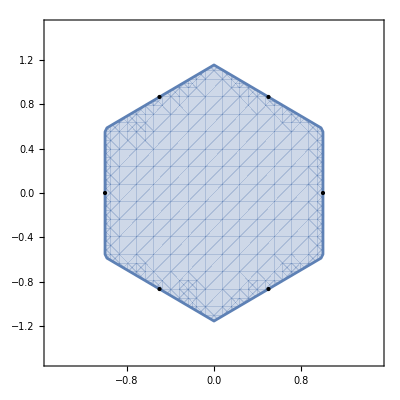

```mathematica
p[i_,n_]:= {Cos[i 2π/n], Sin[i 2 π/n]}
n=6;
RegionPlot[And[
p[1,n].(p[1,n]-{x1,x2})≥0,
p[2,n].(p[2,n]-{x1,x2})≥0,
p[3,n].(p[3,n]-{x1,x2})≥0,
p[4,n].(p[4,n]-{x1,x2})≥0,
p[5,n].(p[5,n]-{x1,x2})≥0,
p[6,n].(p[6,n]-{x1,x2})≥0
],
{x1,-1.5,1.5},
{x2,-1.5,1.5},
Epilog->Point[Table[p[i,n],{i,1,n}]]]
```

## Algorithmic Differentiation

### Basic Example

This is much clearer with an example. The function from f:ℝ^3→ℝ^2
	f[x]={x_3+x_1 x_2,x_1 x_2+Cos[x_1+Sin[x_3]]}
is easy to implement.  Here is code to compute it in small steps with the work variables stored in a sequence of “work” variables.

```mathematica
f[{x1_,x2_,x3_}]:= Module[{w1,w2,w3,w4,w5},
w1=x1*x2;
w2=x3+w1;
w3=Sin[x3];
w4=x1+w3;
w5=Cos[w4];
{w2,w5}
]
```

Functions always need to be tested.  This is far from a complete test!

```mathematica
x={0.2,1.4,0.6};
f[x]
```

Here is a forward mode Algorithmic Differentiation (AD) code for the function.

```mathematica
df[{x1_,x2_,x3_},{dx1_,dx2_,dx3_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5},
dw1=dx1*x2+x1*dx2;
w1=x1*x2;
dw2=dx3+dw1;
w2=x3+w1;
dw3=Cos[x3]*dx3;
w3=Sin[x3];
dw4=dx1+dw3;
w4=x1+w3;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];
{{w2,w5},{dw2,dw5}}
]
```

We need to test this trick.

{{-0.68,0.934251},{-4.6,-0.572774}}

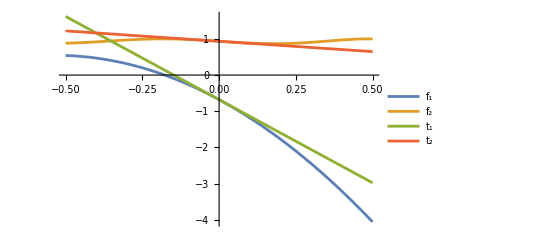

```mathematica
x={0.2,-0.4,-0.6};
dx={1.2,-3.6,-3.4};
{{f1,f2},{df1,df2}}=df[x,dx]
Plot[{f[x+ h dx]⟦1⟧,f[x+ h dx]⟦2⟧,
f1+h df1,f2+h df2},
{h, -0.5,0.5},
PlotLegends->{"f_1","f_2","t_1","t_2"}]
```

They look like tangent lines to me.   The AD code produces accurate derivatives!

```mathematica
n=3;
{x0,dx0}=RandomReal[{-1,1},{2,n}];
Gradf[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}];
Df0=Gradf[x0].dx0
{f0,df0}=df[x0,dx0]
Df0-df0
```

{-0.38824,-0.353241}

{{-0.0185541,0.833228},{-0.38824,-0.353241}}

{0.,0.}

The centered difference produces reasonably accurate derivatives IF we use a good value for “h”.

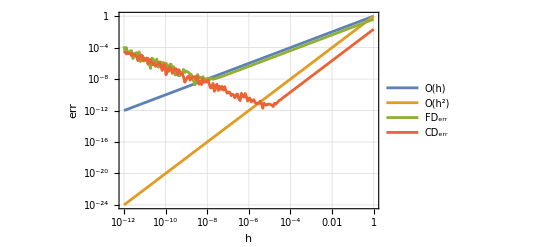

```mathematica
LogLogPlot[{
h,h^2,
Norm[Df0-(f[x0+h dx0]-f[x0])/h],
Norm[Df0-(f[x0+h dx0]-f[x0-h dx0])/(2h)]
},{h, 10^-12, 1},
GridLines->Automatic,Frame->True,FrameLabel->{"h","err"},
PlotLegends->{"O(h)","O(h^2)","FD_err","CD_err"},
MaxRecursion->2]
```

You can do the same thing again top get a directional second derivatives as well.  Real time example!

```mathematica
ddf[{x1_,x2_,x3_},{dx1_,dx2_,dx3_},
{dy1_,dy2_,dy3_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5,
ddw1,ddw2,ddw3,ddw4,ddw5},

ddw1=dx1*dy2+dy1*dx2;
dw1=dx1*x2+x1*dx2;
w1=x1*x2;

ddw2=0.0+ddw1;
dw2=dx3+dw1;
w2=x3+w1;

ddw3=-Sin[x3]*dy3*dx3;
dw3=Cos[x3]*dx3;
w3=Sin[x3];

ddw4=0.0+ddw3;
dw4=dx1+dw3;
w4=x1+w3;

ddw5=-Cos[w4]*dw4*dw4-Sin[w4]*ddw4;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];

{{w2,w5},{dw2,dw5},{ddw2,ddw5}}
]
```

```mathematica
x={0.2,-0.4,-0.6};
dx={1.2,-3.6,-3.4};
dy={-1.2,3.2,3.1};
{{f1,f2},{df1,df2},{ddf1,ddf2}}=ddf[x,dx,dy];
Gradf[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}];
GradGradf[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3},2}];
```

```mathematica
ddf2
```

-4.53241

```mathematica
Clear[h,g]
D[D[f[x+h dx + g dy],h],g]/.{h->0,g->0}
```

{8.16,-0.0837925}

```mathematica
D[Gradf[x+ g dy].dx,g]/.g->0.0
{ddf1,ddf2}
```

{8.16,-0.0837925}

{8.16,-4.53241}

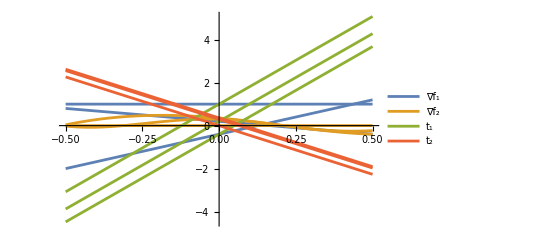

```mathematica
Plot[{(Gradf[x+ g dy].dx)⟦1⟧,(Gradf[x+ g dy].dx)⟦2⟧,
df1+g ddf1,df2+g ddf2},
{g, -0.5,0.5},
PlotLegends->{"∇f_1","∇f_2","t_1","t_2"}]
```

```mathematica
Plot[{f[x+ h dx]⟦1⟧,f[x+ h dx]⟦2⟧,
f1+h df1,f2+h df2},
{h, -0.5,0.5},
PlotLegends->{"f_1","f_2","t_1","t_2"}]
```

-Graphics-